```mathematica
a=Range[1980,1996,2]
```

{1980,1982,1984,1986,1988,1990,1992,1994,1996}

```mathematica
b={338.7,341.1,344.4,347.2,351.5,354.2,356.4,358.9,362.6}
```

{338.7,341.1,344.4,347.2,351.5,354.2,356.4,358.9,362.6}

```mathematica
{338.7,341.1,344.4,347.2,351.5,354.2,356.4,358.9,362.6}
```

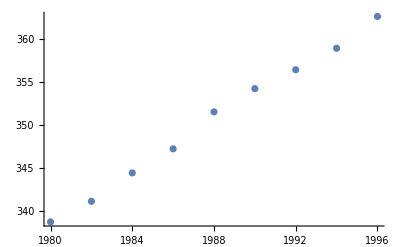

```mathematica
lp1=ListPlot[{{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6}}]
```

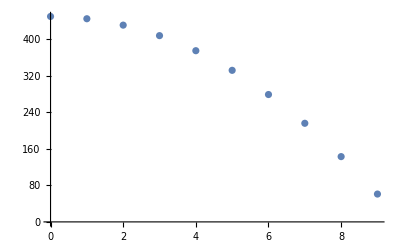

```mathematica
ListPlot[{{0,450},{1,445},{2,431}, {3,408},{4,375},{5,332}, {6, 279},{7,216},{8,143},{9,61}}]
```

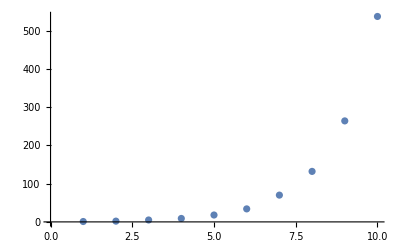

```mathematica
lp3=ListPlot[{{1, 1},{2,2},{3,5},{4,9},{5,18},{6,34},{7,70},{8,132},{9,264},{10,537}}]
```

```mathematica
m:={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6}}
p[x_]:=a*x+b
Err1[a_,b_]:=Sum[ (m[[i,2]]-p[m[[i,1]]])^2 ,{i,1,9}]
```

```mathematica
sol1:=NSolve[{D[Err1[a,b],a]==0,D[Err1[a,b],b]==0},{a,b}]//Simplify
```

```mathematica
p1[x_]:=p[x]/.sol1[[1]]
```

```mathematica
p1[x]
```

-2631.44+1.5 x

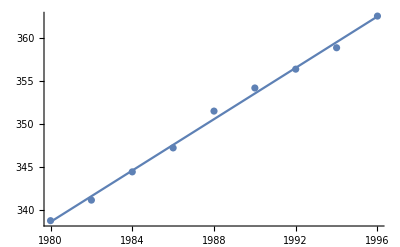

```mathematica
Show[Plot[p1[x],{x,1980,1996}],lp1]
```

```mathematica
n:={{1, 1},{2,2},{3,5},{4,9},{5,18},{6,34},{7,70},{8,132},{9,264},{10,537}}
f[x_]:=a*E^x+b
Err2[a_,b_]:=Sum[ (n[[i,2]]-f[n[[i,1]]])^2 ,{i,1,10}]
```

```mathematica
sol2:=NSolve[{D[Err2[a,b],a]==0,D[Err2[a,b],b]==0},{a,b}]
```

```mathematica
p2[x_]:=f[x]/.sol2[[1]]
```

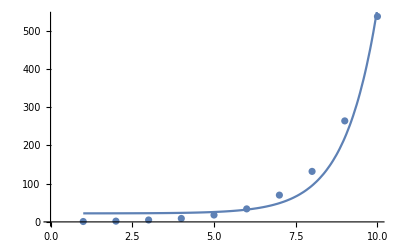

```mathematica
Show[lp3,Plot[p2[x],{x,1,11}]]
```